```mathematica
SWs = Table[i,{i,2,8}];
```

```mathematica
Nt = 647;(*151*)
ti = 0; tf =5; 
deltat = (tf - ti) /Nt ;
xi = -40; xf = 40;
Nx = 455;
deltax = (xf - xi) / Nx;
c = 1;
(*maxErrLD2 = Table[0,{i,1,Length[Nxs]}];*)
maxErrPI = Table[0,{i,1,Length[SWs]}];
(*maxEnergyLD2 = Table[0,{i,1,Length[Nxs]}];*)
maxEnergyPI = Table[0,{i,1,Length[SWs]}];
(*maxProbLD2 = Table[0,{i,1,Length[Nxs]}];*)
maxProbPI = Table[0,{i,1,Length[SWs]}];

(*maxevalsLD2 = Table[0,{i,1,Length[SWs]}];
maxevalsRK2 = Table[0,{i,1,Length[rs]}];*)
maxevalsPI = Table[0,{i,1,Length[SWs]}];

f[x_] = ⅇ^(- x^2+ⅈ x);
T = N[Table[tn = ti + n *deltat, {n, 0, Nt -1 }],32];

Subscript[δ, i_,j_]:=KroneckerDelta[i,j];

(************************************************************************************************************************)
(*Set Up*)
(************************************************************************************************************************)

Xp= N[Table[xm = xi + m *deltax, {m, 0, Nx}],32];

Xo = N[Table[xn = xi + n *deltax, {n, 0, Nx -1}],32];

L2 = N[Table[(NDSolve`FiniteDifferenceDerivative[Derivative[i],Xp, "DifferenceOrder"->6, PeriodicInterpolation->True]@"DifferentiationMatrix"//Normal), {i,1,8}],32];
DL2 = L2[[2]] * deltat * (ⅈ / 2);
```

```mathematica
(*LD2*)
ULD2= N[Table[0, {n, 1, Nt}, {m, 1, Nx}],32];
ULD2[[1,All]] = N[f[Xo],32];
ULD2 = Chop[ULD2, 10^(-307)];
ULD2 = Developer`ToPackedArray[ULD2, Complex]; 
Developer`PackedArrayQ[ULD2];

ILD2 = N[IdentityMatrix[Length[DL2]],32];
ALD2 = N[ILD2 - (DL2 / 2),32];
BLD2 = N[ILD2 + (DL2 / 2),32];
MLD2 = N[Inverse[ALD2].BLD2,32];
EMLD2 = N[MLD2 - ILD2,32];
EMLD2 = Developer`ToPackedArray[EMLD2, Real]; 

Do[ULD2[[n+1,All]] = ULD2[[n,All]] + (EMLD2).ULD2[[n,All]], {n,1,Nt - 1 }];

(*LD2*)
FLD2 = Table[0,{i,1,Nt},{j,1,Nx}];
FLD2 = Developer`ToPackedArray[FLD2, Real];
intLD2 = Table[0,{i,1,Length[FLD2[[All,1]]]}];
intLD2 = Developer`ToPackedArray[intLD2, Real];
GLD2 = Table[0,{i,1,Nt},{j,1,Nx}];
GLD2 = Developer`ToPackedArray[GLD2, Real];
GintLD2 = Table[0,{i,1,Length[FLD2[[All,1]]]}];
GintLD2 = Developer`ToPackedArray[GintLD2, Real];
Do[
FLD2[[i]] = Conjugate[ULD2[[i,All]]](ULD2[[i,All]])//Re;

intLD2[[i]] = (2π)/Nx Total[FLD2[[i,All]]];
GLD2[[i]] = -0.5Conjugate[ULD2[[i,All]]](L2[[2]].ULD2[[i,All]])//Re;

GintLD2[[i]] = (2π)/Nx Total[GLD2[[i,All]]]
,{i,1,Length[FLD2[[All,1]]]}];

probErrorLD2=Abs[GintLD2-GintLD2[[1]]];
energyErrorLD2 = Abs[intLD2 - intLD2[[1]]];

maxProbLD2 = Max[probErrorLD2];
maxEnergyLD2 = Max[energyErrorLD2];


fexact[t_,x_] = 1/(√(1+2 ⅈ t))Exp[(-(x-ⅈ/2)^2)/(1+2ⅈ t)-1/4];
Uexact = Table[fexact[T[[i]],Xo[[j]]],{i,1,Nt},{j,1,Nx}];
Uexact = Chop[N[Uexact], 10^(-307)];
Uexact = Developer`ToPackedArray[Uexact, Complex];

exacti={Re[fexact[0,Xo]],Im[fexact[0,Xo]]}//Transpose;

exactf={Re[fexact[T[[-1]],Xo]],Im[fexact[T[[-1]],Xo]]}//Transpose;

(*LD2*)
abserrLD2 = Abs[ULD2-Uexact];
errorLD2 = Table[0,{i,1,Length[abserrLD2]}];
errorLD2 = Developer`ToPackedArray[errorLD2, Real];
Do[
errorLD2[[i]] = Norm[abserrLD2[[i,All]], 1] * deltax;
,{i,1,Length[errorLD2]}
];

maxErrLD2 = Max[errorLD2];
```

```mathematica
Do[
(*Partial Inversion*)
UP= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
UP[[1,All]] = N[f[Xo],32];
UP = Chop[UP, 10^(-307)];
UP = Developer`ToPackedArray[UP, Complex]; 
Developer`PackedArrayQ[UP];


selectwidth = SWs[[p]];
diffOrder = 6;

deriv = 2;

(*The total number of points in the stencil*)
totalpoints = (2*selectwidth) + 1;

(*The middle point in the stencil*)
middlepoint = selectwidth + 1;

(*Set up the grid for the stencil*)
grid=x0+(Range[totalpoints]-middlepoint)Δx;

(LP=NDSolve`FiniteDifferenceDerivative[Derivative[deriv],grid,"DifferenceOrder"->diffOrder]@"DifferentiationMatrix"//Normal);

(*define r:=Δt/(Δx^deriv)*)
(*This is done so the M Matrix can be created symbollically and be created for any CFL Number by putting in a value for r*)
r=.;
LPX = LP*((-1)^deriv)*(r*(Δx)^deriv);

(*Manualy set up periodic boundary conditions because PeriodicInterpolation will remove removes a grid point on the end*)
(*Can use PeriodicInterpolation on the L Matrix if you add a +1 when defining the grid*)
gn = (LPX[[middlepoint,All]]//Normal)//Simplify//FullSimplify;
LPX = Table[RotateRight[gn,i],{i,-selectwidth,selectwidth}];
LPX[[1,-1]]=0;
LPX[[1,-2]]=0;
LPX[[2,-1]]=0;
LPX[[-1,1]]=0;
LPX[[-1,2]]=0;
LPX[[-2,1]]=0;
LPX[[-3,1]] = 0;
LPX[[-2,2]] = 0;
LPX[[-1,3]] = 0;
LPX[[1,-3]] = 0;
LPX[[2,-2]] = 0;
LPX[[3,-1]] = 0;
LPX = LPX//.{r -> (deltat / (deltax)^deriv)};

(*Set up Identity Matrix*)
IP=IdentityMatrix[Length[LPX]];

(*Generate a Crank–Nicolson M Matrix for the stencil*)
(Mn=Inverse[IP-(ⅈ * LPX)/4 ].(IP+(ⅈ * LPX)/4));

(*Take the middle row from this Crank-Nicolson M Matrix*)
fn=(Mn[[middlepoint,All]]//Normal)//Simplify//FullSimplify;


(*Generate a M Matrix from the L matrix for the stencil*)
MP = Table[0,{i,1,Nx},{j,1,Nx}];

(*WITHOUT Periodic Boundary Conditions Placed*)
MP = Table[Sum[(Subscript[δ, i,j+(middlepoint-k)])fn[[k]] + (Subscript[δ, i,(j-k)])fn[[middlepoint + k]],{k,selectwidth}] + Subscript[δ, i,j] fn[[middlepoint]],{i,1,Nx},{j,1,Nx}];

(*WITH Periodic Boundary Conditions*)
(*MP = Table[Sum[(Subscript[δ, i,j+(middlepoint-k)])fn[[k]] + (Subscript[δ, i,(j-k)])fn[[middlepoint + k]],{k,selectwidth}] + Subscript[δ, i,j] fn[[middlepoint]] + Sum[(Subscript[δ, (i + Nx) - n,j])fn[[selectwidth - (n - 1)]] + (Subscript[δ, (i + Nx) + n,(j + 2*Nx)])fn[[(middlepoint + 1) + (n - 1)]]  ,{n,1,selectwidth}],{i,1,Nx},{j,1,Nx}];*)

Ip = IdentityMatrix[Length[MP]];

EMP = MP - Ip;

EMP= Developer`ToPackedArray[EMP, Real]; 

Do[UP[[n+1,All]] = UP[[n,All]] + (EMP).UP[[n,All]], {n,1,Nt - 1 }];


(************************************************************************************************************************)
(*Energy and Prob*)
(************************************************************************************************************************)

(*Partial Inversion*)
FP= Table[0,{i,1,Nt},{j,1,Nx}];
FP = Developer`ToPackedArray[FP, Real];
intP = Table[0,{i,1,Length[FP[[All,1]]]}];
intP = Developer`ToPackedArray[intP, Real];
GP= Table[0,{i,1,Nt},{j,1,Nx}];
GP = Developer`ToPackedArray[GP, Real];
GintP = Table[0,{i,1,Length[FP[[All,1]]]}];
GintP = Developer`ToPackedArray[GintP, Real];
Do[
FP[[i]] = Conjugate[UP[[i,All]]](UP[[i,All]])//Re;

intP[[i]] = (2π)/Nx Total[FP[[i,All]]];
GP[[i,All]] =-0.5 Conjugate[UP[[i,All]]](L2[[2]].UP[[i,All]])//Re;

GintP[[i]] = (2π)/Nx Total[GP[[i,All]]]
,{i,1,Length[FP[[All,1]]]}];


probErrorP = Abs[GintP - GintP[[1]]];

energyErrorP = Abs[intP - intP[[1]]];


maxProbPI[[p]] = Max[probErrorP];

maxEnergyPI[[p]] = Max[energyErrorP];


(************************************************************************************************************************)
(*L1 Error*)
(************************************************************************************************************************)

(*Partial Inversion*)
abserrP = Abs[UP-Uexact];
errorP = Table[0,{i,1,Length[abserrP]}];
errorP = Developer`ToPackedArray[errorP, Real];
Do[
errorP[[i]] = Norm[abserrP[[i,All]], 1] * deltax;
,{i,1,Length[errorP]}
];

maxErrPI[[p]] = Max[errorP];


Print["Finished " <> ToString[SWs[[p]]]];


,{p,1,Length[SWs]}]
```

Finished 2

Finished 3

Finished 4

Finished 5

Finished 6

Finished 7

Finished 8

```mathematica
maxEnergyLD2Constant = Table[maxEnergyLD2,{i,1,Length[SWs]}]
maxProbLD2Constant = Table[maxProbLD2,{i,1,Length[SWs]}]
maxErrLD2Constant = Table[maxErrLD2,{i,1,Length[SWs]}]
```

{4.996×10^-16,4.996×10^-16,4.996×10^-16,4.996×10^-16,4.996×10^-16,4.996×10^-16,4.996×10^-16}

{5.68989×10^-16,5.68989×10^-16,5.68989×10^-16,5.68989×10^-16,5.68989×10^-16,5.68989×10^-16,5.68989×10^-16}

{0.760892,0.760892,0.760892,0.760892,0.760892,0.760892,0.760892}

```mathematica
(*ListLogPlot[{probErrorLD2,probErrorP, probErrorRK2},PlotStyle->{Blue, Red, Green},PlotLegends->{"LD2","PI", "RK2"}]*)
```

```mathematica
(*ListLogPlot[{Transpose[{T,energyErrorLD2}], Transpose[{T,energyErrorP}], Transpose[{T,energyErrorRK2}]},PlotStyle->{Blue, Red, Green},PlotLegends->{"LD2","PI", "RK2"},AxesLabel->{"T","Log(|Relative Energy Error)"},PlotLabel->"Relative Energy Error",PlotRange->{{ti,tf},All},Joined->True]*)
```

```mathematica
(*ListLogPlot[{Transpose[{T,errorLD2}],Transpose[{T,errorP}],Transpose[{T,errorRK2}]},PlotRange->{{ti,tf},All}, PlotStyle->{Blue,{Red, Dashed}, Green},PlotLegends->{"LD2","PI", "RK2"},AxesLabel->{"T","Log(L1 Error)" },PlotLabel->"L1 Error", Joined->True]*)
```

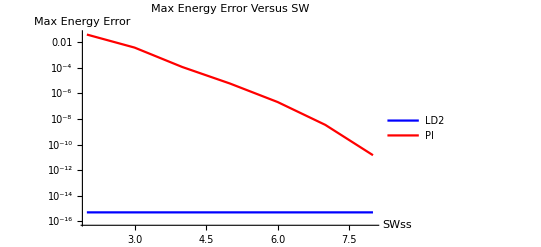

```mathematica
ListLogPlot[{Transpose[{SWs,maxEnergyLD2Constant}], Transpose[{SWs,maxEnergyPI}]},PlotStyle->{Blue, Red},PlotLegends->{"LD2","PI"},AxesLabel->{"SWss","Max Energy Error"},PlotLabel->"Max Energy Error Versus SW",PlotRange->{All,All},Joined->True]
```

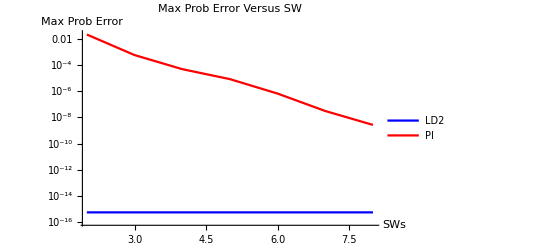

```mathematica
ListLogPlot[{Transpose[{SWs,maxProbLD2Constant}], Transpose[{SWs,maxProbPI}]},PlotStyle->{Blue, Red},PlotLegends->{"LD2","PI"},AxesLabel->{"SWs","Max Prob Error"},PlotLabel->"Max Prob Error Versus SW",PlotRange->{All,All},Joined->True]
```

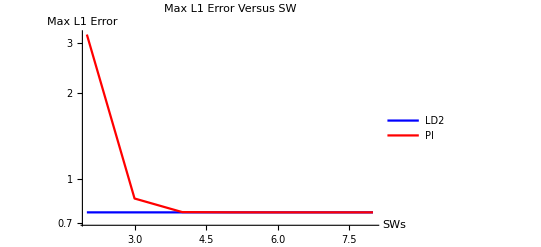

```mathematica
ListLogPlot[{Transpose[{SWs,maxErrLD2Constant}], Transpose[{SWs,maxErrPI}]},PlotStyle->{Blue, Red},PlotLegends->{"LD2","PI"},AxesLabel->{"SWs","Max L1 Error"},PlotLabel->"Max L1 Error Versus SW",PlotRange->{All,All},Joined->True]
```

```mathematica
maxErrLD2
```

0.760892

```mathematica
maxErrPI
```

{3.20918,0.851266,0.762566,0.761146,0.760885,0.760891,0.760892}

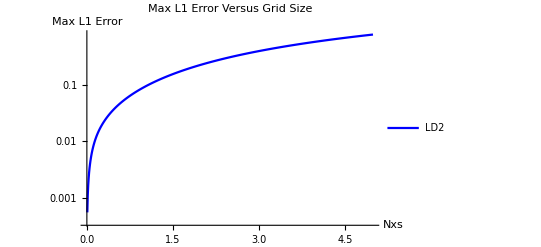

```mathematica
ListLogPlot[{Transpose[{T,errorLD2}]},PlotStyle->{Blue, Red},PlotLegends->{"LD2","PI"},AxesLabel->{"Nxs","Max L1 Error"},PlotLabel->"Max L1 Error Versus Grid Size",PlotRange->{All,All},Joined->True]
```

```mathematica
ψ[t_,x_]=1/(√(1+2 ⅈ t))Exp[(-(x-ⅈ/2)^2)/(1+2ⅈ t)-1/4]
```

(ⅇ^(-1/4-(-ⅈ/2+x)^2/(1+2 ⅈ t)))/(√(1+2 ⅈ t))

```mathematica
D[ψ[t,x], t]//FullSimplify
```

-(ⅇ^((t-2 x-2 ⅈ x^2)/(2 ⅈ-4 t)) (-3 ⅈ+4 t+4 x+4 ⅈ x^2))/(2 (ⅈ-2 t)^2 √(1+2 ⅈ t))

```mathematica
(-1/(2ⅈ))*D[ψ[t,x], {x,2}]//FullSimplify
```

-(ⅇ^((t-2 x-2 ⅈ x^2)/(2 ⅈ-4 t)) (-3 ⅈ+4 t+4 x+4 ⅈ x^2))/(2 (ⅈ-2 t)^2 √(1+2 ⅈ t))